Morrey p. 144.
df(x,h)=f'(x)·h.

```mathematica
f1[x_]:=x^2
```

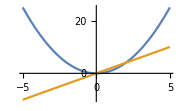

```mathematica
Plot[{f1[x],2x},{x,-5,5},ImageSize->Small]
```

```mathematica
D[f1[x],x]
```

2 x

Multiplicação de derivadas/funções.

```mathematica
Table[D[f1[x],x]*h,{h,0,5}]
```

{0,2 x,4 x,6 x,8 x,10 x}

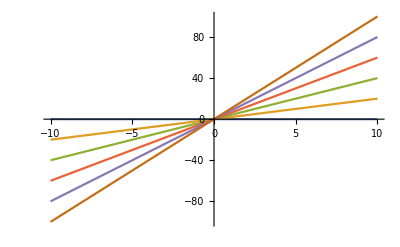

```mathematica
Plot[{0,2 x,4 x,6 x,8 x,10 x},{x,-10,10}]
```

Estes são os diferenciais de f(x)=x^2:
df(x,h)=2x·h,
executados para diversos h (multiplicador).
O multiplicador é o segundo parâmetro do diferencial, logo o diferencial é uma família de funções multiplicadas da derivada da função.

```mathematica
Plot3D[2x*h,{x,-10,10},{h,-10,10},ImageSize->Medium]
```

-Graphics3D-

Esse é o diferencial de x^2 variando as duas variáveis.

```mathematica
D[Sin[x],x]
```

Cos[x]

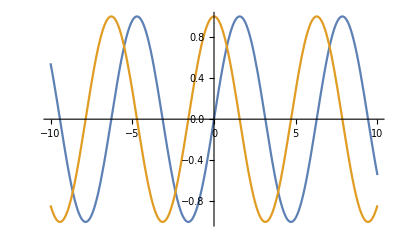

```mathematica
Plot[{Sin[x],Cos[x]},{x,-10,10}]
```

```mathematica
Plot3D[Cos[x]*h,{x,-100,100},{h,-100,100},ImageSize->Medium]
```

-Graphics3D-

Mas o fato de ser uma função de duas variáveis/plot tridimensional é apenas incidental. Ele é um criador de uma família da derivada de f. Inclusive, uma das funções da família é a própria derivada.
Para f(x)=sin x,
df(x,h)=cos x·h.

```mathematica
Table[Cos[x]*h,{h,-3,3,1}]
```

{-3 Cos[x],-2 Cos[x],-Cos[x],0,Cos[x],2 Cos[x],3 Cos[x]}

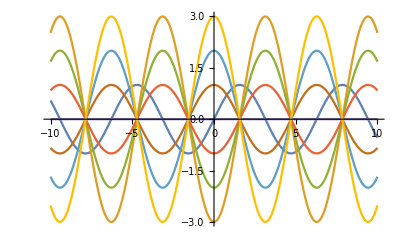

```mathematica
Plot[{Sin[x],-3 Cos[x],-2 Cos[x],-Cos[x],0,Cos[x],2 Cos[x],3 Cos[x]},{x,-10,10}]
```

```mathematica
f3[x_]=x^2+2x+4
```

4+2 x+x^2

```mathematica
D[f3[x],x]
```

2+2 x

```mathematica
Table[(2+2x)*h,{h,-3,3,1}]
```

{-3 (2+2 x),-2 (2+2 x),-2-2 x,0,2+2 x,2 (2+2 x),3 (2+2 x)}

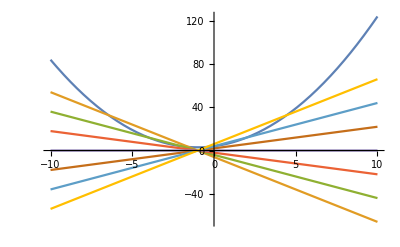

```mathematica
Plot[{x^2+2x+4,-3 (2+2 x),-2 (2+2 x),-2-2 x,0,2+2 x,2 (2+2 x),3 (2+2 x)},{x,-10,10}]
```

Se f(x)=x^2+2x+4,
df(x)=(2x+2)·h.

O diferencial num ponto é uma família de multiplicadores da derivada (naquele ponto) (e um deles é a derivada). Os demais diferem mais ou menos da derivada.

h é x_1

Então se f(x)=x^2+2x+4,
f'(x)=(y_1-y_0)/(x_1-x_0)=(f(x_1)-f(x_0))/(x_1-x_0)=...

Assumir x_1=x_0+Δx é expressar o numerador somente em termos de x_0.

(f(x_0+Δx)-f(x_0))/(x_1-x_0)=((x_0+Δx)^2+2(x_0+Δx)+4-(x_0^2+2 x_0+4))/(x_0+Δx-x_0)=
(x_0^2+2 x_0 Δx+Δx^2+2 x_0+2Δx+4-x_0^2-2 x_0-4)/Δx=(2 x_0 Δx+Δx^2+2Δx)/Δx=
(Δx(2 x_0+Δx+2))/Δx=2 x_0+Δx+2, que tende a 2 x_0+2 conforme Δx tende a zero.

Aqui, não temos mais x_1 na função, exceto na forma de Δx=x_1-x_0 que tende a zero.

x_1-x_0 tende a zero porque x_1 se aproxima de x_0, mas enquanto x_1≠0, df(x,x_1)≠f'(x).

```mathematica
Manipulate[Plot[{x^2,2x*h},{x,-10,10},PlotRange->{{-5,5},{-10,10}}],{h,-10,10,.5}]
```

Mas aqui eu estou manipulando f'(x)·h... e não f'(x+x_1) (?).
Esses são os possíveis diferenciais, para qualquer x_1.
Agora preciso manipular x_1.

```mathematica
Table[D[x^2+Subscript[x, 0],x],{Subscript[x, 0],1,5}]
```

{2 x,2 x,2 x,2 x,2 x}

A derivada é fixa para apenas diferenças de constante, mas o diferencial varia.
O diferencial é ignorar a anulação das constantes?

Por isso o diferencial não é derivar f(x)+x_1... É multiplicar f'(x) por x_1.
O manipulate acima está correto... é só
1) Desenhar o x_1 referente;
2) Deslocar o diferencial (o que pode ser uma forma de referenciar o x_1) em proporção a x_1.
Depois que fizer isso, poderei desenhar a derivada para comparar com o diferencial.

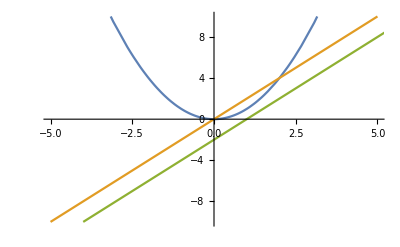

```mathematica
Plot[{x^2,2x,2x-2},{x,-10,10},PlotRange->{{-5,5},{-10,10}}]
```

Como deslocar horizontalmente a função em proporção a um x?

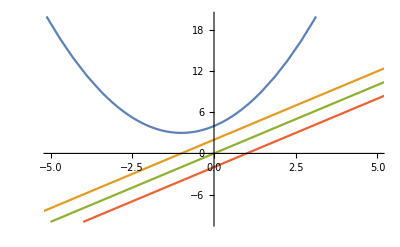

```mathematica
Plot[{x^2+2x+4,2x+2,2x+2-2,2x-2},{x,-10,10},PlotRange->{{-5,5},{-10,20}}]
```

f(x)=2x+2
f(x)+2=2x+2⇒
f(x)=2x

Eu acho que essa correção não vai (mas poderia) fazer tangenciar o diferencial.

```mathematica
Table[(2x*h)-h,{h,-5,5}]
```

{5-10 x,4-8 x,3-6 x,2-4 x,1-2 x,0,-1+2 x,-2+4 x,-3+6 x,-4+8 x,-5+10 x}

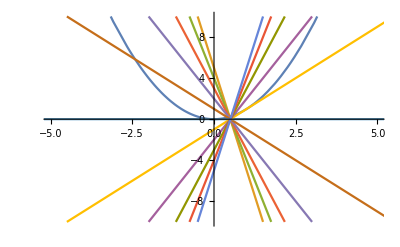

```mathematica
Plot[{x^2,5-10 x,4-8 x,3-6 x,2-4 x,1-2 x,0,-1+2 x,-2+4 x,-3+6 x,-4+8 x,-5+10 x},{x,-10,10},PlotRange->{{-5,5},{-10,10}}]
```

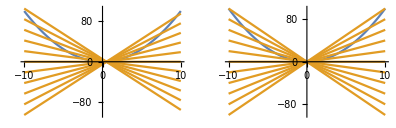

```mathematica
GraphicsRow[{
Plot[{x^2,Table[(2x*h)-h,{h,-5,5}]},{x,-10,10},ImageSize->Small],
Plot[{x^2,Table[(2x*h),{h,-5,5}]},{x,-10,10},ImageSize->Small]
}]
```

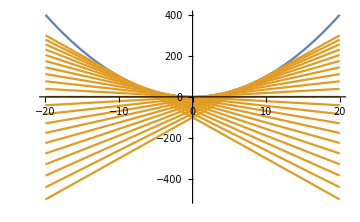

```mathematica
Plot[{x^2,Table[(2x*h)-h^2,{h,-10,10}]},{x,-20,20},ImageSize->Medium]
```

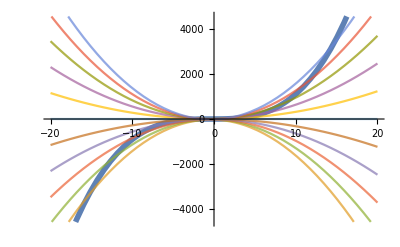

```mathematica
Plot[{x^3+x^2+x,Evaluate[Table[(D[x^3+x^2+x,x]*h)-h^2,{h,-5,5}]]},{x,-20,20},PlotStyle->Flatten[{m,Table[s,11]}]]
```

```mathematica
D[x^3+x^2+x,x]
```

1+2 x+3 x^2

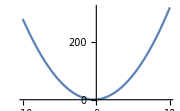

```mathematica
Plot[1+2 x+3 x^2,{x,-10,10},ImageSize->Small]
```

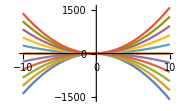

```mathematica
Plot[Evaluate[Table[(1+2 x+3 x^2)*a,{a,-5,5,1}]],{x,-10,10},ImageSize->Small]
```

Um, já sabemos que a multiplicação da parábola a agudece, ou suaviza até inverter a concavidade...

O que está parecendo é que o diferencial é uma fórmula arbitrária, e que o h (multiplicador) deve ser de grau 1 menor que o da função.

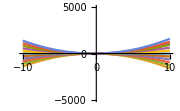
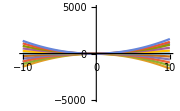
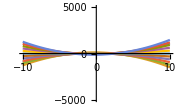
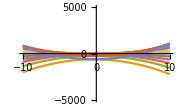
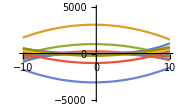
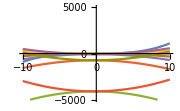
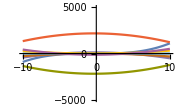
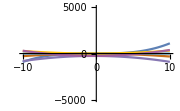

```mathematica
Table[Plot[{x^3+x^2+x,Evaluate[Table[((1+2 x+3 x^2)*h)-h^n,{h,-5,5,1}]]},{x,-10,10},ImageSize->Small,PlotRange->{{-10,10},{-5000,5000}}],{n,1,8,1}]
```

```mathematica
D[x^4+x^3+x^2+x,x]
```

1+2 x+3 x^2+4 x^3

```mathematica
Table[((1+2 x+3 x^2+4 x^3)*h)-h,{h,-5,5,1}]
```

{5-5 (1+2 x+3 x^2+4 x^3),4-4 (1+2 x+3 x^2+4 x^3),3-3 (1+2 x+3 x^2+4 x^3),2-2 (1+2 x+3 x^2+4 x^3),-2 x-3 x^2-4 x^3,0,2 x+3 x^2+4 x^3,-2+2 (1+2 x+3 x^2+4 x^3),-3+3 (1+2 x+3 x^2+4 x^3),-4+4 (1+2 x+3 x^2+4 x^3),-5+5 (1+2 x+3 x^2+4 x^3)}

```mathematica
Table[((1+2 x+3 x^2+4 x^3)*h)-h^2,{h,-5,5,1}]
```

{-25-5 (1+2 x+3 x^2+4 x^3),-16-4 (1+2 x+3 x^2+4 x^3),-9-3 (1+2 x+3 x^2+4 x^3),-4-2 (1+2 x+3 x^2+4 x^3),-2-2 x-3 x^2-4 x^3,0,2 x+3 x^2+4 x^3,-4+2 (1+2 x+3 x^2+4 x^3),-9+3 (1+2 x+3 x^2+4 x^3),-16+4 (1+2 x+3 x^2+4 x^3),-25+5 (1+2 x+3 x^2+4 x^3)}

```mathematica
Table[((1+2 x+3 x^2+4 x^3)*h)-h^3,{h,-5,5,1}]
```

{125-5 (1+2 x+3 x^2+4 x^3),64-4 (1+2 x+3 x^2+4 x^3),27-3 (1+2 x+3 x^2+4 x^3),8-2 (1+2 x+3 x^2+4 x^3),-2 x-3 x^2-4 x^3,0,2 x+3 x^2+4 x^3,-8+2 (1+2 x+3 x^2+4 x^3),-27+3 (1+2 x+3 x^2+4 x^3),-64+4 (1+2 x+3 x^2+4 x^3),-125+5 (1+2 x+3 x^2+4 x^3)}

```mathematica
m=Directive[Opacity[1],Thickness[.01]]
s=Directive[{Opacity[.7]}]
```

Directive[Opacity[1],Thickness[0.01]]

Directive[{Opacity[0.7]}]

Família de derivadas de f de grau n=4 (grau 3) multiplicadas por constantes elevadas a 1 (n-3)

```mathematica
Flatten[{m,Table[s,11]}]
```

{Directive[Opacity[1],Thickness[0.01]],Directive[{Opacity[0.7]}],Directive[{Opacity[0.7]}],Directive[{Opacity[0.7]}],Directive[{Opacity[0.7]}],Directive[{Opacity[0.7]}],Directive[{Opacity[0.7]}],Directive[{Opacity[0.7]}],Directive[{Opacity[0.7]}],Directive[{Opacity[0.7]}],Directive[{Opacity[0.7]}],Directive[{Opacity[0.7]}]}

```mathematica
Prepend[Table[s,11],m]
```

{Directive[Opacity[1],Thickness[0.01]],Directive[{Opacity[0.7]}],Directive[{Opacity[0.7]}],Directive[{Opacity[0.7]}],Directive[{Opacity[0.7]}],Directive[{Opacity[0.7]}],Directive[{Opacity[0.7]}],Directive[{Opacity[0.7]}],Directive[{Opacity[0.7]}],Directive[{Opacity[0.7]}],Directive[{Opacity[0.7]}],Directive[{Opacity[0.7]}]}

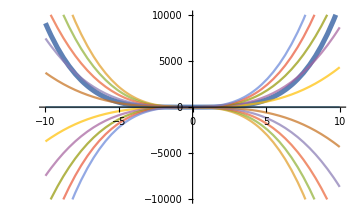

```mathematica
Plot[{x^4+x^3+x^2+x,5-5 (1+2 x+3 x^2+4 x^3),4-4 (1+2 x+3 x^2+4 x^3),3-3 (1+2 x+3 x^2+4 x^3),2-2 (1+2 x+3 x^2+4 x^3),-2 x-3 x^2-4 x^3,0,2 x+3 x^2+4 x^3,-2+2 (1+2 x+3 x^2+4 x^3),-3+3 (1+2 x+3 x^2+4 x^3),-4+4 (1+2 x+3 x^2+4 x^3),-5+5 (1+2 x+3 x^2+4 x^3)},{x,-10,10},PlotRange->{{-10,10},{-10000,10000}},ImageSize->Medium,PlotStyle->Prepend[Table[s,11],m]]
```

Família de derivadas de f de grau n=4 (grau 3) multiplicadas por constantes elevadas a 2 (n-2)

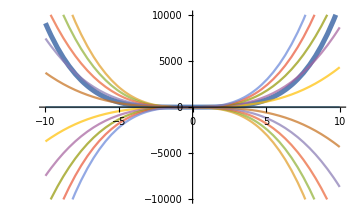

```mathematica
Plot[{x^4+x^3+x^2+x,-25-5 (1+2 x+3 x^2+4 x^3),-16-4 (1+2 x+3 x^2+4 x^3),-9-3 (1+2 x+3 x^2+4 x^3),-4-2 (1+2 x+3 x^2+4 x^3),-2-2 x-3 x^2-4 x^3,0,2 x+3 x^2+4 x^3,-4+2 (1+2 x+3 x^2+4 x^3),-9+3 (1+2 x+3 x^2+4 x^3),-16+4 (1+2 x+3 x^2+4 x^3),-25+5 (1+2 x+3 x^2+4 x^3)},{x,-10,10},PlotRange->{{-10,10},{-10000,10000}},ImageSize->Medium,PlotStyle->Prepend[Table[s,11],m]]
```

Família de derivadas de f de grau n=4 (grau 3) multiplicadas por constantes elevadas a 3 (n-1)

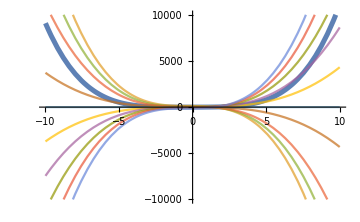

```mathematica
Plot[{x^4+x^3+x^2+x,125-5 (1+2 x+3 x^2+4 x^3),64-4 (1+2 x+3 x^2+4 x^3),27-3 (1+2 x+3 x^2+4 x^3),8-2 (1+2 xF+3 x^2+4 x^3),-2 x-3 x^2-4 x^3,0,2 x+3 x^2+4 x^3,-8+2 (1+2 x+3 x^2+4 x^3),-27+3 (1+2 x+3 x^2+4 x^3),-64+4 (1+2 x+3 x^2+4 x^3),-125+5 (1+2 x+3 x^2+4 x^3)},{x,-10,10},PlotRange->{{-10,10},{-10000,10000}},ImageSize->Medium,PlotStyle->Prepend[Table[s,11],m]]
```

Comparando as famílias de derivadas.

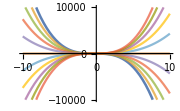
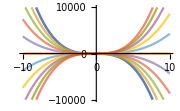
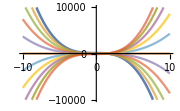
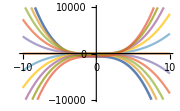
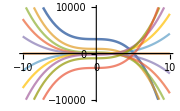
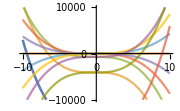
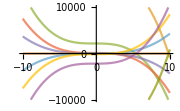
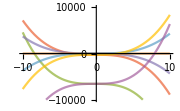

```mathematica
Table[Plot[Evaluate[Table[((1+2 x+3 x^2+4 x^3)*h)-h^n,{h,-5,5,1}]],{x,-10,10},ImageSize->Small,PlotRange->{{-10,10},{-10000,10000}},PlotStyle->Prepend[Table[s,11],m]],{n,1,12,1}]
```

Tudo isso era tentativa de entender 1.. Mas não parece ser reproduzível. Tentei  deslocar cada diferencial de acordo com x subtraindo x de f'. Porém isso resulta na mesma subtração para todo f', pelo menos no gráfico. Mesmo sendo subtraído h, que varia. (O motivo é que h é igual à constante de f'.)

Tangenciamento da derivada da parábola

Dada uma parábola x^2 e a derivada 2x...

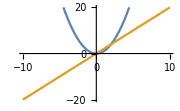

```mathematica
Plot[{x^2,2x},{x,-10,10},ImageSize->Small,PlotRange->{{-10,10},{-20,20}}]
```

A derivada é o limite conforme Δx→0=x_1-x_0→0.
Silverman p. 55. “The derivative f'(x_0) is just the slope of the tangent to the curve f(x) at the point with abscissa x_0.”

Então a questão é que cada ponto tem uma derivada que é um número, mas este número não é a secante, ele é a razão instantânea entre y e x na função, e essa razão é o slope da linha secante.

Então em x=5, f'(x)=10 e a secante é y=10x. (I had completely forgotten this!)
Em x=10, f'(x)=20 e a secante é y=20x.
f'(20)=40⇒y=40x;
f'(30)=60⇒y=60x.

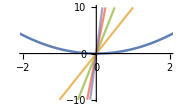

```mathematica
Plot[{x^2,10x,20x,40x,60x},{x,-10,10},ImageSize->Small,PlotStyle->Prepend[Table[s,4],m],PlotRange->{{-2,2},{-10,10}},PlotLegends->"Expressions"]
```

Agora, como deslocar estas secantes. Em x=5, a secante 10x... f(5)=25.
Precisamos da secante de slope 10x que passa por y=25.
Mas a secante em x=5 é 50. 50-25=25. Na verdade é subtração de y de f pelo da secante. 25-50=-25.
Outra... Em x=10, f(10)=100, f'(10)=200. 100-200=-100.

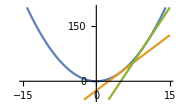

```mathematica
Plot[{x^2,10x-25,20x-100},{x,-15,15},ImageSize->Small,PlotRange->{{-15,15},{-50,200}}]
```

Agora fazer o mesmo para os diferenciais.

Silverman:
1) Havendo derivada, a derivada é onde o ratio chega a zero.
2) Se o ratio chega a zero, o ratio variável menos o ratio final (a derivada) tende a zero.
3) Os dois ratios são sobre a mesma quantidade, a diferença em x, que chega a zero. Logo, se um ratio (o da derivada) se estabiliza em um valor, o outro ratio (variável) também se estabiliza em um valor.
4) A diferença nos valores em que se estabilizam é pequena (tende a zero) por 2). (?) Logo, um é uma boa aproximação do outro.
Está errado. O diferencial não é um ratio, é uma quantidade no eixo y (imagem), assim como o incremento (Δy). A diferença entre os dois tende a zero conforme o incremento no eixo x (Δx) tende a zero.

Nota: para cada x, há uma derivada e um diferencial.

df(x,h)=
f'(x)·h=
(lim_(Δx→0) Δy/Δx)·h=
lim_(Δx→0) (Δy/Δx·h)=
lim_(Δx→0) ((Δy·hΔx)/Δx).

Δy é o incremento.
Δy=f(x+Δx)-f(x).

Para x^2, Δy=y_1-y_0=f(x_1)-f(x_0)=f(x_0+Δx)-f(x_0). (Estava correto.)
Para x_0=5, Δy=x_1^2-25=(x_0+Δx)^2-25=(5+Δx)^2-25=Δx^2
25+10Δx+Δx^2-25=Δx^2+10Δx.
lim_(Δx→0) ((x_1^2-25)·5)/(x_1-5)=lim_(Δx→0) (Δx^2·5)/(x_0+Δx-5)=lim_(Δx→0) (5 Δx^2)/Δx=lim_(Δx→0) 5Δx=5.

Errado. O limite apenas permite afirmar a proximidade do diferencial com a derivada. Mas ele “some” da equação do diferencial, porque é igualado a zero (?). A equação diz:

lim_(Δx→0) (Δy·hΔx)/Δx=0.
Onde h=x_1. Errado. h=Δx.

Mas eu comecei do ponto errado. Reboot (Silverman).

f'(x)=lim_(Δx→0) Δy/Δx⇒
(lim_(Δx→0) Δy/Δx)-f'(x)=0⇒
lim_(Δx→0) (Δy/Δx-f'(x))=0⇒
lim_(Δx→0) Δy/Δx-
(não é para processar f'(x))
lim_(Δx→0) (Δy-f'(x)Δx)/Δx=0.

Agora, sim... A diferença entre Δy/Δx e (Δy-f'(x)Δx)/Δx ou melhor,
Δy/Δx-(Δy-f'(x)Δx)/Δx=(Δy-Δy+f'(x)Δx)/Δx=(f'(x)Δx)/Δx=f'(x).

Mas não é esse o ponto. Porque não é a diferença absoluta entre a derivada e esta razão: a derivada é o valor/limite quando Δx→0, e o limite desta razão é zero. O ponto é que ambas as razões são um limite sobre (“denominador”) a mesma quantidade, Δx. Sendo tal, a atenção se volta ao numerador. E aí

Δy-(Δy-f'(x)Δx)=f'(x)Δx, ou seja, (o numerador da) segunda razão apenas é diferente (do numerador da) derivada em f'(x)Δx.
Considerando que o limite da derivada conforme Δx→0 tende a um n e o limite da segunda razão conforme Δx→0 é 0, elas não são absolutamente iguais.
Mas, considerando globalmente que a diferença entre as duas é f'(x)Δx...

df/dx=f'(x);
df=dy=f'(x)Δx.
Δy=f(x+Δx)-f(x).

A comparação é entre o incremento e o diferencial... não entre a derivada e o diferencial. Por isso, a comparação entre os numeradores... porque o numerador da derivada é o incremento.

Ou seja, eu preciso passar a visualizar não só o diferencial, mas o incremento...

Agora sim, temos uma comparação par a par, porque o incremento e o diferencial são das mesmas variáveis, x_0 e x_1.
É inclusive necessário escrever ambos em termos destas variáveis pois atribuiremos um x_0 em comum entre os dois e variaremos x_1.

f'(x)=(f(x_1)-f(x_0))/(x_1-x_0).
df(x)=(f(x_1)-f(x_0))/(x_1-x_0)·(x_1-x_0).

Para f(x)=x^2 e x_0=5, 
f'(x)=2x e 
df(x)=2x·(x_1-5).

Nota: o limite que tende a 0 não é a diferença entre a derivada e o diferencial. O diferencial surge desta diferença, que é entre a derivada e a derivada (?).

O diferencial é o valor da derivada multiplicado pelo deslocamento em x.
O incremento (Δy) com relação à derivada?
A derivada é Δy/Δx. A razão entre os incrementos em y e x.
O incremento é o valor exato da mudança em y dado um Δx.
O diferencial é um valor aproximado da mudança em y dado o mesmo Δx.
Se sabemos a derivada e sabemos Δx, sabemos o incremento em Δx.
E o diferencial é calculado a partir da derivada, portanto ela não é prescindível.

Mas sabendo uma derivada, como calculo um incremento?
Supondo f(x)=x^2, f'(x)=2x.
f'(x)=Δy/Δx, para Δx=5, 2x=Δy/5⇒
Δy=10x.
Mais rigorosamente...
f'(x_0)=(y_1-y_0)/(x_1-x_0). Para x_0=2 e x_1=7, 
2 x_0=(y_1-y_0)/5⇒
y_1-y_0=10 x_0...
Preciso primeiro derivar x^2 com x_0 e x_1.
f'(x_0)=(y_1-y_0)/(x_1-x_0)=(f(x_1)-f(x_0))/(x_1-x_0)(Limite)=lim_(x_1→x_0) (x_1^2-x_0^2)/(x_1-x_0). Essa é uma boa fórmula.
Para x_0=2, f'(2)=lim_(x_1→2) (x_1^2-4)/(x_1-2). Boas fórmulas!
Agora sim estabelecendo x_1=x_0+Δx, 
f'(2)=lim_(x_0+Δx→2) ((x_0+Δx)^2-4)/((x_0+Δx)-2)=
lim_(2+Δx→2) ((2+Δx)^2-4)/((2+Δx)-2)=
O quê ocorreu aqui? A substituição de x_1 por x_0 (que é conhecido) + um valor desconhecido deixa a função apenas em função do valor desconhecido.
Por algum motivo, isso vem a eliminar/agrupar a fórmula em torno do valor desconhecido, por ele estar presente em todos os termos (não eliminados) do numerador, e no denominador.
=lim_(Δx→0) (4Δx+Δx^2)/Δx=
lim_(Δx→0) 4+Δx=
4.
Esse valor desconhecido é também o valor especificado no limite, reduzindo a fórmula a um número.

Mas a pergunta é... o incremento é apenas (neste caminho)
Δy=
y_1-y_0=
f(x_1)-f(x_0).
Para x_0=5,
Δy=f(x_1)-f(5)=
f(x_1)-25=
f(x_0+Δx)-25=
f(5+Δx)-25=
(5+Δx)^2-25=
25+10Δx+Δx^2-25=
10Δx+Δx^2?

```mathematica
deltay1[deltax_]:=10*deltax+deltax^2
```

```mathematica
Table[deltay1[deltax],{deltax,{2,5,15}}]
```

{24,75,375}

Esses são todos incrementos para x_0=5.

Quais são os incrementos, com mesmo Δx, para x_0=9?

Δy=Δy(x_0)=
O incremento é apenas uma função sobre x_0...
f(x_0+Δx)-f(x_0)=
f(9+Δx)-f(9)=
(9+Δx)^2-81=
81+18Δx+Δx^2-81=
18Δx+Δx^2.

```mathematica
deltay2[deltax_]:=18*deltax+deltax^2
```

```mathematica
Table[deltay2[deltax],{deltax,{2,5,15}}]
```

{40,115,495}

(Visualizar os incrementos)

Agora, ao invés dos incrementos, vamos calcular os diferenciais nos mesmos x_0 e para os mesmos Δx.

Primeiro, quais foram as características do cálculo dos incrementos? Foi necessário executar a função duas vezes, uma algebricamente (realizando fatoração algébrica) e outra numericamente, para se chegar na função Δy para se executar (numericamente) para cada Δx.

1) A fórmula do diferencial, resgatar porquê ela é assim.
2) Executá-la.
3) Plotar incrementos, diferenciais, e compará-los.

#### Funções

Primeiro, o incremento é uma função de uma função, um x_0 e um x_1 (sendo Δx=x_1-x_0, ou seja:
Δf(f,x_0,x_1)=f(x_0+(x_1-x_0))-f(x_0)=f(x_1)-f(x_0) ou
Δf(f,x_0,Δx)=f(x_0+Δx)-f(x_0).

A derivada é uma função de f, x_0, o incremento, e o mesmo Δx. Ou, absolutamente, 
A derivada é uma função de f, x_0, x_1, igualmente.
f'(f,x_0,x_1)=(f(x_0+(x_1-x_0))-f(x_0))/(x_1-x_0)=(f(x_1)-f(x_0))/(x_1-x_0) ou
f'(f,x_0, Δx)=(f(x_0+Δx)-f(x_0))/Δx.

O incremento é a medida do deslocamento em y para f e x_0 e x_1.
A derivada é a razão do incremento para o deslocamento entre x_1 e x_0.
De forma similar, o “diferencial” tem um incremento?
f'(x)·Δx=f(x_0+Δx)-f(x_0)=f(x_1)-f(x_0)?
O diferencial é só o numerador da derivada? Se for, é igual a Δy.
Piskunov, p. 114: “A derivada pode ser considerada a razão do diferencial de y com o diferencial de x”.
Δy=dy+αΔx.
Sendo αΔx a diferença entre o incremento e o diferencial de y=f.
Ou seja, o diferencial não é Δy.
Tanto x quanto y têm um diferencial.
α implicando a diferença entre os dois, o que é α?
α é a diferença entre Δy/Δx e lim_(Δx→0) Δy/Δx enquanto Δx>0.

```mathematica
Clear[fratiodeltas]
fratiodeltas[f_,x0_,x1_]:=(f[x1]-f[x0])/(x1-x0)
```

```mathematica
Table[fratiodeltas[Function[x,x^2],2,x1],{x1,{3,6,11}}]
```

{5,8,13}

```mathematica
Limit[fratiodeltas[Function[x,x^2],2,x1],x1->0]
```

2

Vemos que 5, 8 e 13 são valores da razão que tendem a 2.

```mathematica
Table[fratiodeltas[Function[x,x^2],2,x1],{x1,{1,0.5,0.1,0.0001}}]
```

{3,2.5,2.1,2.0001}

Vamos plotar esta tendência.

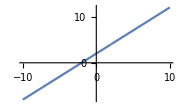

```mathematica
Plot[fratiodeltas[Function[x,x^2],2,x1],{x1,-10,10},ImageSize->Small]
```

Obviamente, eu estou apenas plotando a derivada da função em x_0=2...

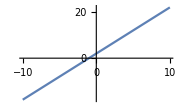

```mathematica
Plot[2x+2,{x,-10,10},ImageSize->Small]
```

Mas uma coisa é que infinitesimal não deveria ser uma função não-linear?

Talvez eu esteja plotando a razão e o infinitesimal é só o numerador...

```mathematica
Clear[fdeltay]
fdeltay[f_,x0_,x1_]:=f[x1]-f[x0]
```

```mathematica
Table[fdeltay[Function[x,x^2],2,x1],{x1,{5,3,2.5,2.001}}]
```

{21,5,2.25,0.004001}

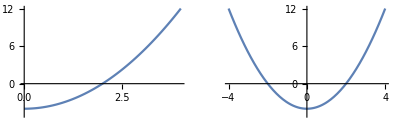

```mathematica
GraphicsRow[{
Plot[fdeltay[Function[x,x^2],2,x1],{x1,0,4},ImageSize->Small,PlotRange->{{0,4},{-5,12}}],
Plot[fdeltay[Function[x,x^2],2,x1],{x1,-4,4},ImageSize->Small,PlotRange->{{-4,4},{-5,12}}]
}]
```

Agora sim...
Wtf are we visualizing here? O incremento em y (Δy) conforme x_1 se aproxima de x_0.
No eixo x, conforme x_1 se aproxima de 2, Δy se aproxima de 0.
Mas o vértice da parábola não está em 2.

Esse gráfico, claro, é apenas o da função f(x)... Mas é “deslocada” na imagem em x_0=2... Tem um deslocamento de f(2)=2^2 na imagem.

```mathematica
GraphicsRow[{
Plot[x^2-4,{x,0,4},ImageSize->Small,PlotRange->{{0,4},{-5,12}}],
Plot[x^2-4,{x,-4,4},ImageSize->Small,PlotRange->{{-4,4},{-5,12}}]
}]
```

-Graphics-

Então no caso desta função deslocada (x_0=2), o incremento Δy tende a -4 conforme x_1 tende a 0.

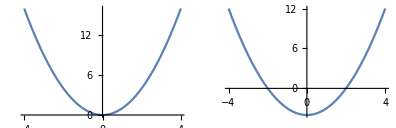

```mathematica
GraphicsRow[{
Plot[x^2,{x,-4,4},ImageSize->Small],
Plot[fdeltay[Function[x,x^2],2,x1],{x1,-4,4},ImageSize->Small]
}]
```

A relação entre a função e o seu incremento...
Se a função não for deslocada (x_0=0), são idênticos...

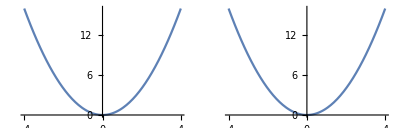

```mathematica
GraphicsRow[{
Plot[x^2,{x,-4,4},ImageSize->Small],
Plot[fdeltay[Function[x,x^2],0,x1],{x1,-4,4},ImageSize->Small]
}]
```

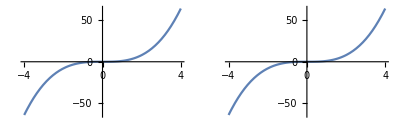

```mathematica
GraphicsRow[{
Plot[x^3,{x,-4,4},ImageSize->Small],
Plot[fdeltay[Function[x,x^3],0,x1],{x1,-4,4},ImageSize->Small]
}]
```

Ou seja, o incremento é y=f variado ao longo do domínio, em termos relativos: ele varia conforme varia x_0.

O que f absolutamente não faz... Δy é um espelho de f, deslocado em imagem por x_0.

Agora vem o diferencial de y.
Se Δy=dy+αΔx,
dy=αΔx-Δy.

O diferencial de y não existe.
y=f(x).
Δy=Δf(x)=f(x_1)-f(x_0).
O diferencial de y é o diferencial de f (assim como a derivada é a derivada de f... mas a derivada é de y/x, e o diferencial é de y, mas y depende de x — y é como um x modificado).
O diferencial de x não existe, também (pois só existe o de f como um todo), a não ser no caso de x ser considerado como f, como veremos, para explicar dy/dx.
Apesar disso, o diferencial de f é um número, assim como f'. Mas o número da derivada expressa uma razão, e o do diferencial não diretamente, mas indiretamente,  estando contido no diferencial a derivada. O diferencial é uma multiplicação arbitrária da derivada, por uma constante “que funciona” (Δx), em termos de aproximar os números.
O fato dos dois números se aproximarem é devido ao limite na definição da derivada:
f'(x)=lim_(Δx→0) Δy/Δx
“A derivada é o limite da razão”. Por simples álgebra,
⇒(lim_(Δx→0) Δy/Δx)-f'(x)=0
Agora a propriedade decisiva.
⇒lim_(Δx→0) (Δy/Δx-f'(x))=0
Esta “associatividade” transforma o limite que era da derivada apenas no da equação.
Agora podemos fatorar o “limitando”.
⇒lim_(Δx→0) (Δy-f'(x)Δx)/Δx=0
Aqui há uma informação importante.
Ia dizer que o numerador e denominador tendem à igualdade, mas não é verdadeiro... seria se a razão tendesse a 1.
Δx tende a zero. Quando Δx “chegar a zero”, ou melhor, nunca chegará, mas conforme Δx se aproxima de zero, Δy-f'(x)Δx se aproxima do que seria, com Δx=0, Δy. E a equação toda se aproxima de Δy/Δx, que “em” ou “conforme” Δx→0, é exatamente a derivada.

Ou seja, conforme, nesta equação, Δx→0, a razão tende à derivada.
E, como a diferença entre a razão e a derivada é apenas o numerador, Δy-f'(x)Δx→Δy.
Como Δy é o incremento, temos uma quantidade que tende ao incremento (no mesmo “ponto”).
Podemos dar um nome a esta quantidade, “diferencial”.
Mas ela não é derivável diretamente do incremento, nem vice-versa (não são “análogos” de “nada”).

O incremento deriva diretamente da função, x_0, e x_1.
O diferencial deriva de uma propriedade dos limites sobre a definição da derivada.
Ou seja, o diferencial vem depois da derivada. Até por isso, ele contém a derivada na sua definição.
Isso significa que o diferencial (na sua aplicação) não evita o cálculo da derivada.
Ele “economiza computação” de outra forma.

Vamos imaginar que precisamos calcular as tangentes, ou secantes, de uma série de pontos em uma função.
Poderemos fazer:
Em x_0=a, f'(a)=lim_(Δx→0) Δy/(x_1-a).
Em x_1=b, f'(b)=lim_(Δx→0) Δy/(x_1-b).
Em x_0=c, f'(c)=lim_(Δx→0) Δy/(x_1-c), etc.
Mas, tendo que...

Primeiro, como conforme Δx→0 dy/Δx→Δy/Δx, (além de dy→Δy), essa outra razão também tende à derivada. Portanto é uma boa aproximação da derivada no mesmo x_0.

Tendo que dy/Δx→Δy/Δx, podemos calcular este. Vamos olhar o que é dy.
dy=f'(x)·Δx.

O valor de dy, que é próximo a Δy... Nomenclatura completa.

dy=f'(x_0)·(x_1-x_0).
Para calcular a derivada, precisamos calcular uma derivada em cada x_0 ou exatamente nos pontos desejados.
Para calcular o diferencial, podemos fixar um x_0 qualquer e “sobra” a variável Δx=x_1-x_0. Podemos calcular a derivada para x_0 uma vez e calcular os Δx e portanto os diferenciais:

Em x_0=a, f'(a)=γ.
Em x_1=b, dy=f'(a)·Δx=γ·(b-a).
Em x_1=c, dy=f'(b)·Δx=γ·(c-a).
Em x_1=d, dy=f'(c)·Δx=γ·(d-a).

Estamos calculando apenas uma subtração e multiplicação.
(Testar em plot.)

#### df=dy ou df=dy/Δx?

Já não ficou claro de novo.

O limite da subtração de duas razões é zero.
Portanto, as duas razões tendem à igualdade (no limite).
As duas razões têm denominador igual.
Isso significa que os numeradores tendem à igualdade (no limite)?
Se sim,
dy/Δx→Δy/Δx conforme Δx→0 e 
dy→Δy conforme Δx→0.

Sim, mas talvez não seja essa a equivalência entre dy e Δy.
Aparentemente, há duas coisas sendo chamadas de diferencial.
Uma é uma razão, que tende à derivada.
A outra, é só o numerador, que tende ao incremento.
Aparentemente, as duas são verdade, mas qual é o diferencial?
Se o diferencial é uma multiplicação (família) da derivada, é a razão.
Se o diferencial é f'(x)·Δx, é o numerador.
Agora ficou aparente... f'(x)Δx=dy é família da derivada. dy/Δx (a razão) não.
Mas agora a pergunta se coloca como sendo o numerador o que tende à derivada, dy/Δx→Δy/Δx conforme Δx→0. Isso deve ser falso, porque dy→Δy/Δx.
Vou deixar essa indagação por aqui (considerando df=dy).

#### Continuando

```mathematica
Clear[f1,f1der,f1points]
f1=Function[x,x^2]
f1der=Function[x,Evaluate[D[f1[x],x]]]
f1points={.5,.8,1.2,2,3.4}
```

Function[x,x^2]

Function[x,2 x]

{0.5,0.8,1.2,2,3.4}

Primeiro as derivadas (translatadas)...

Primeiro os slopes em cada x_0.

```mathematica
Clear[f1ders]
f1ders=Table[f1der[x0],{x0,f1points}]
```

{1.,1.6,2.4,4,6.8}

```mathematica
f1der[2]
```

4

Depois, as funções dos slopes (secantes).
O slope é y/x. Logo se y/x=n, y=xn.
Em x=0.5, o slope é 1. Logo y/n=1⇒y=n. A função slope é s(x)=x.
Em x=0.8, o slope é 1.6. Logo y/n=1.6⇒y=1.6n. A função slope é s(x)=1.6x.

```mathematica
Clear[MakeSlope]
MakeSlope=Function[x,Evaluate[Function[n,n*x]]]
```

Function[x,Function[n,n x]]

```mathematica
MakeSlope[2][x]
```

2 x

```mathematica
MakeSlope[f1der[2]][x]
```

4 x

```mathematica
Clear[slopefs]
slopefs=Table[MakeSlope[f][x],{f,f1ders}]
```

{1. x,1.6 x,2.4 x,4 x,6.8 x}

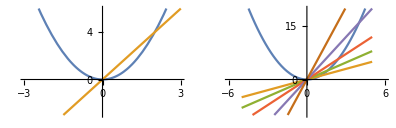

```mathematica
GraphicsRow[{
Plot[{x^2,2x},{x,-5,5},PlotRange->{{-3,3},{-3,6}},ImageSize->Small],
Plot[{x^2,slopefs},{x,-5,5},PlotRange->{{-6,6},{-10,20}},ImageSize->Small]
}]
```

```mathematica
Clear[slopes]
slopes=Table[MakeSlope[f1der[n]][x],{n,f1ders}]
```

{2. x,3.2 x,4.8 x,8 x,13.6 x}

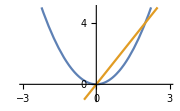
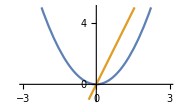
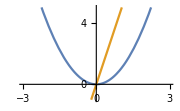
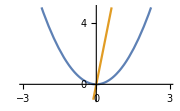
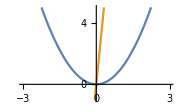

```mathematica
Table[Plot[{f1[x],tf},{x,-5,5},PlotRange->{{-3,3},{-1,5}},ImageSize->Small],{tf,slopes}]
```

Graficamente, isto está batendo (funções slope)? Um caso bom é o x_0=2.
Em x_0=2, f'(2)=2·2=4. A função slope é f(x)=4x.

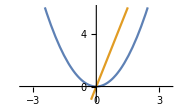

```mathematica
Plot[{x^2,4x},{x,-5,5},PlotRange->{{-3.5,3.5},{-1,6}},ImageSize->Small]
```

Parece ok.

Agora, as funções deslocadas dos slopes (tangentes).

A translação é a diferença entre o y de f(x_0) e o y de s(x_0), em que s é a função slope da derivada f'(x_0).
Não... a translação é... Eu preciso que a reta s passe por um ponto (x,y) definido por f. x está definido e é o valor onde foi tirada a derivada (x_0). Com esse x tenho yde f, e substituo na equação de s:

Em x_0=2,
f(2)=2^2=4.
y/x=4⇒y=s=4x.
Talvez seja diferença de x naquele y.
Sabemos que f(2)=4. Mas se quiser calcular x, 4=x^2⇒x=2.
Agora mesmo para s.
4=4x⇒x=1.

Agora eu tenho a diferença entre o x em que a derivada (secante) está no y em que eu quero (tangenciar) e o x=x_0 em que a derivada foi tomada.

É só deslocar a derivada (secante) por esta diferença.
A diferença está em x; é preciso converter x em y em termos de s para saber a diferença em y, que é o que será somado a s (pois somamos à variável independente).
Δx=2-1=-1.
s(-1)=4·-1=-4.
t(x)=4x-4.

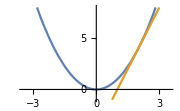

```mathematica
Plot[{x^2,4x-4},{x,-10,10},PlotRange->{{-3.5,3.5},{-1,8}},ImageSize->Small]
```

Suscita a pergunta... não é possível verificar diretamente a diferença em y?

Em x_0=2,
f(2)=2^2=4.
y/x=4⇒y=s=4x.
Agora, y em s é s(2)=8.
Vamos apenas deslocar a imagem de s por essa diferença.
Δy=4-8=-4
=f(x_0)-s(x_0).

Agora vamos fazer este cálculo sumariamente.

Em x_0=2, 
f'(2)=4, 
s=4x, 
f(2)-s(2)=4-8=-4, 
t=s+-4=4x-4.

Em x_0=3.4, 
f'(3.4)=6.8, 
s=6.8x, 
f(3.4)-s(3.4)=11.56-23.12=-11.56, 
t=s+-11.56=6.8x-11.56.

```mathematica
6.8*3.4
```

23.12

```mathematica
11.56-23.12
```

-11.56

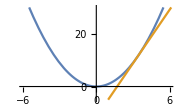

```mathematica
Plot[{x^2,6.8x-11.56},{x,-10,10},PlotRange->{{-6,6},{-5,30}},ImageSize->Small]
```

```mathematica
f1der
Clear[f1x0,f1x0s,f1x0ydif,f1x0t]
f1x0=3.4
f1der[f1x0]
f1x0s=MakeSlope[f1der[f1x0]];
f1x0s[x]
f1x0ydif=f1[f1x0]-f1x0s[f1x0]
f1x0t=f1x0s[x]+f1x0ydif
```

Function[x,2 x]

3.4

6.8

6.8 x

-11.56

-11.56+6.8 x

```mathematica
Plot[{f1[x],f1x0t},{x,-10,10},PlotRange->{{-6,6},{-5,30}},ImageSize->Small]
```

-Graphics-

```mathematica
Clear[GetTangent]
GetTangent[f_,x0_]=Module[{fder,der,s,ydif,t},
	fder=Function[x,Evaluate[D[f[x],x]]];
	der=fder[x0];
	s=MakeSlope[der];
	ydif=f[x0]-s[x0];
	t=s[x]+ydif;
	t
];
```

```mathematica
Clear[f1x0t]
f1x0t=GetTangent[Function[x,x^2],2]
```

-4+4 x

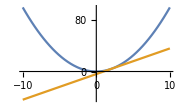

```mathematica
Plot[{x^2,f1x0t},{x,-10,10},ImageSize->Small]
```

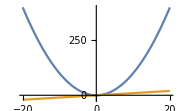
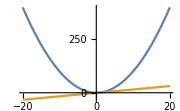
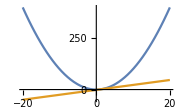
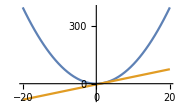
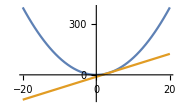

```mathematica
Table[Plot[{f1[x],GetTangent[f1,x0]},{x,-20,20},ImageSize->Small],{x0,f1points}]
```

```mathematica
GetTangent[Function[x,x^2],γ]
```

2 x γ-γ^2

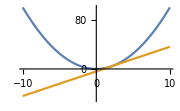
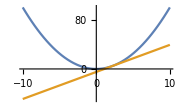
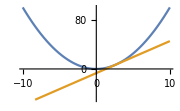
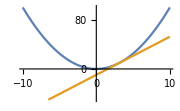
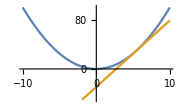
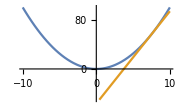

```mathematica
Table[Plot[{f1[x],GetTangent[f1,x0]},{x,-10,10},ImageSize->Small,PlotRange->{{-10,10},{-50,100}}],{x0,{2,2.2,2.6,3.1,5.4,7.5}}]
```

Agora os diferenciais.

Estamos tomando as derivadas em diversos x_0 (executando a função GetTangent(), que é a ‘computação’). Agora iremos fixar um x_0, tomar a derivada e calcular os diferenciais com Δx em função deste x_0.
Em x_0=2, f'(2)=4.
O diferencial está definido como dy=f'(x_0)·Δx.
Para x_1=2, dy=4·(2-2)=0. (?)
Para x_1=5.4, dy=4·(5.4-2)=13.6.

```mathematica
4*(5.4-2)
```

13.6

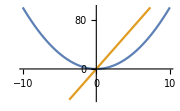

```mathematica
Plot[{x^2,13.6x},{x,-10,10},ImageSize->Small,PlotRange->{{-10,10},{-50,100}}]
```

O diferencial tem de ser deslocado assim como a derivada! (?)

Vamos chamar o diferencial “secante” de ds e o diferencial “tangente” de ts.
Em ds=13.6x, y=ds(5.4)=73.44.
f(5.4)=29.16.
f(x_0)-ds(x_0)=-44.28.
Então iremos deslocar verticalmente o diferencial por isto.

```mathematica
5.4*13.6
```

73.44

```mathematica
5.4^2
```

29.16

```mathematica
29.16-73.44
```

-44.28

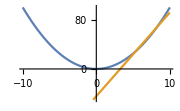

```mathematica
Plot[{x^2,13.6x-44.28},{x,-10,10},ImageSize->Small,PlotRange->{{-10,10},{-50,100}}]
```

Seems it worked?

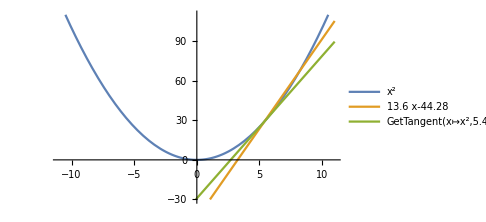

```mathematica
Plot[{x^2,13.6x-44.28,GetTangent[Function[x,x^2],5.4]},{x,-11,11},ImageSize->Medium,PlotRange->{{-11,11},{-30,110}},PlotLegends->"Expressions"]
```

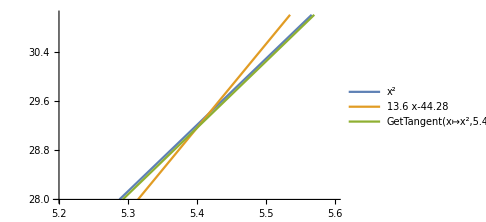

```mathematica
Plot[{x^2,13.6x-44.28,GetTangent[Function[x,x^2],5.4]},{x,-11,11},ImageSize->Medium,PlotRange->{{5.2,5.6},{28,31}},PlotLegends->"Expressions"]
```

Parece que sim pois se cruzam em x_0.
E, agora, para outro x_1 (ainda na mesma derivada)...
Para x_1=2.2, dy=4·(2.2-2)=0.8.
ds(2.2)=0.8x.
f(2.2)-ds(2.2)=3.08.
dt(2.2)=0.8x+3.08.

```mathematica
4*(2.2-2)
```

0.8

```mathematica
(2.2^2)-(0.8*2.2)
```

3.08

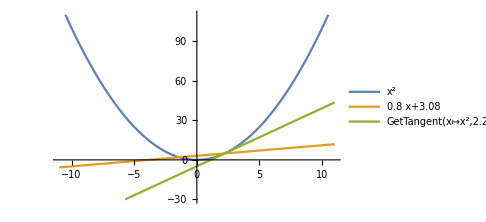

```mathematica
Plot[{x^2,0.8x+3.08,GetTangent[Function[x,x^2],2.2]},{x,-11,11},ImageSize->Medium,PlotRange->{{-11,11},{-30,110}},PlotLegends->"Expressions"]
```

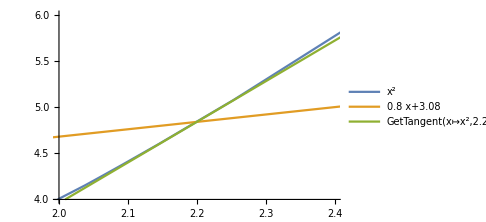

```mathematica
Plot[{x^2,0.8x+3.08,GetTangent[Function[x,x^2],2.2]},{x,-11,11},ImageSize->Medium,PlotRange->{{2.0,2.4},{4,6}},PlotLegends->"Expressions"]
```

Podemos ver que a derivada e o diferencial não se cruzam em x_0.

E, este diferencial está muito diferente da derivada.

Se, por exemplo, eu tomasse a derivada em x_0=3 e Δx fosse 2.4 (x_1=5.4), o diferencial seria igual?
f'(3)=6x.
ds=6x·2.4=14.4x.

```mathematica
6*2.4
```

14.4

Não. São curvas diferentes, e apenas estou tangenciado no mesmo ponto, curvas arbitrárias.

A minha dúvida (que me fez pensar em diferencial “relativo” e não “fixado” em x_0) era como tomaríamos o diferencial, se ele é infinitesimalmente pequeno conforme Δx→0. Isso significa que não poderíamos tomar Δx=0, o que faríamos, tomaríamos um Δx arbitrariamente pequeno? (Eu odiaria este arbítrio.)

Acontece que sim. O diferencial é tomado em um x_0 (igual ao da derivada) e multiplica a derivada por um Δx arbitrariamente pequeno.

Portanto, em x_0=2.2, dy=4.4·0.1=...

O diferencial não substitui a derivada. Substitui o incremento.

Feita a substituição, podemos dividir o diferencial (assim como o incremento) por Δx e obter o slope?

Em x_0=2.2, Δy=f(x_0+Δx)-f(x_0)=...

Ah, entendi. Para a derivada, também, um Δx arbitrariamente pequeno é tomado (para comparar com o diferencial).

Os dois valores ficam aproximados do slope “real” da derivada.

Em x_0=2.2 e com Δx=0.1,
Δy=f(2.2+0.1)-f(2.2)=0.45.
dy=f'(2.2)·0.1=0.44.

```mathematica
f1[2.3]-f1[2.2]
```

0.45

```mathematica
4.4*0.1
```

0.44

Temos agora os slopes?
Δy/Δx=4.5.
dy/Δx=4.4.

E a derivada “real” em x_0=2.2 é 2x(2.2)=4.4. Igual ao diferencial e diferente da derivada “aproximada”.
Estranho que o diferencial não devia ser igual, porque Δx≠0.
Vamos tomar alguns diferenciais de x^2.

```mathematica
Clear[incr]
incr=Function[{f,x0,x1},f[x1]-f[x0]];
incr[Function[x,x^2],2,x1]
```

-4+x1^2

```mathematica
Clear[incrratio]
incrratio=Function[{f,x0,x1},incr[f,x0,x1]/(x1-x0)];
incrratio[Function[x,x^2],2.2,2.3]
```

4.5

```mathematica
Clear[deriv]
deriv=Function[{f,x0},Limit[incrratio[f,x0,x1],x1->x0]];
deriv[Function[x,x^2],10]
```

20

```mathematica
deriv[Function[x,x^2],2.2]
```

4.4

Foi estranho que o slope do diferencial
dy=f'(2.2)·0.1=0.44⇒
ds=0.44/0.1=4.44
ficou igual à derivada
2x(2.2)=4.4.
dy=f'(x_0)·Δx=
2x(2.2)·0.1=
4.4·0.1=0.44⇒
dy/Δx=0.44/0.1=4.4.
Mas vamos primeiro montar a função do diferencial.

```mathematica
Clear[difer]
difer=Function[{f,x0,deltax},deriv[f,x0]*deltax];
```

```mathematica
Table[difer[Function[x,x^2],2.2,deltax],{deltax,{0.0001,0.001,0.01,0.1,1}}]
```

{0.00044,0.0044,0.044,0.44,4.4}

```mathematica
Clear[diferratio]
diferratio=Function[{f,x0,deltax},difer[f,x0,deltax]/deltax];
```

```mathematica
Table[diferratio[Function[x,x^2],2.2,deltax],{deltax,{0.0001,0.001,0.01,0.1,1}}]
```

{4.4,4.4,4.4,4.4,4.4}

Todos os ratios dos diferenciais são iguais à derivada. Why the f*?
Claro... porque estou multiplicando (no diferencial) por Δx e depois dividindo por ele mesmo. Sobra só a derivada, ridículo.
Mas isso não deveria funcionar?

Bom... disto vemos que, como o ratio do diferencial é igual à derivada, dy/Δx=f'. Daí a nomenclatura, mas não só por isso... Porque também o diferencial de x como f(x)=x é
f'(x)=1⇒dy=1·Δx=Δx.
Como dx=Δx, 
dy/Δx=f'=dy/dx. (Resta ver a ressalva citada no Piskunov.)

O ratio do diferencial é igual à derivada porque como ele é um multiplicador por Δx e o ratio um divisor por Δx eles se anulam mas não deveria ser estranhado isso porque o diferencial deriva da derivada, ele “sabe quem a derivada é”.

O que estou tentando fazer é obter o slope do diferencial. Como na derivada ele é a razão (instantânea), no diferencial... se o slope do diferencial (calculado) é igual à derivada, ambos não podem ser a mesma linha. Portanto (por lógica), a razão do diferencial não é o seu slope.
O slope do diferencial é só o diferencial, que entrega a linha proposta. dy/Δx perde o significado de slope. Mas... Δy/Δx é o slope da derivada. E dy/dx=f'=Δy/Δx=dy/Δx? Um não é slope e o outro é.
Se dy/dx é a derivada, que é um slope, e é também dy/Δx, que é a razão do diferencial, que não é um slope, qual está correto? Que dy/dx é dy/Δx está certo. Logo, ou é falso que dy/dx é um slope, ou é falso que dy/Δx não é um slope. Que dy/dx é um slope é verdade, logo é falso que dy/Δx não é um slope. Mas... é falso mesmo, porque dy/Δx é (igual à) derivada, que é um slope. Então de onde eu tirei que dy/Δx não era um slope?
Eu tirei que “se o slope do diferencial é igual à derivada, ambos não podem ser a mesma linha”. “Portanto a razão do diferencial não é seu slope”. Dizer isso diz que a razão do diferencial é igual à derivada. O que é verdade.
Mas se o slope do diferencial (calculado) é igual à derivada, eles são a mesma linha. Portanto, o slope do diferencial não pode ser igual à derivada. Isso implica que suas razões são diferentes.
Mas a razão do diferencial é dy, e a da derivada, dy/Δx. Portanto eles são diferentes.
Mas se eles são diferentes, como dy/dx=dy/Δx? Se isso for verdade, dy/dx=dy.
Há alguma falsidade na afirmação dy/dx=f'=Δy/Δx=dy/Δx. (Tudo isso começou quando estabelecemos dy/Δx=dy/dx.)

Anyways, agora podemos plotar os diferenciais.
Aliás, diferenciais não são ou têm razões. Nem são slopes, linhas, ou podem ser plotados como tal. O “número” que resulta da computação do diferencial em um x_0 NÃO é uma linha. Esse número aproxima o incremento Δy, não a derivada f'=Δy/Δx.
É claro que há uma linha para este incremento, mas ela não é o diferencial, e eu não sei como defini-la.

Piskunov, p. 118: O “incremento” é a mudança em y para um Δx. O diferencial é também uma mudança em y para um Δx, mas de outra função: a tangente/secante/derivada em x_0 (por isso ele é o numerador da derivada — a derivada é uma relação — razão — entre seu próprio y e x e o diferencial é a mudança neste y). O incremento é a mudança na própria função, outro na sua derivada. Em x_0 (a “origem”), os dois são iguais. Conforme se distanciam (Δx aumenta), diferem. A diferença passa a ser o “erro”.
Em um dado x_0, é possível tomar a derivada; mas também é possível, já tendo a derivada naquele ponto, “aproximar” x_1 de x_0, sem alcançá-lo; obtendo um valor próximo. (E porque eu faria isso — ao invés de calcular a derivada?)

Isso parece ter a ver com... como garantimos que em um dado x_0 (diferenciável) a função e sua derivada têm mesmo slope? Garantimos porque a derivada em um x_0 é o slope da função.

A derivada é a “permanência” da taxa de mudança de uma função em um ponto, na forma de uma reta (falando em duas dimensões) (por isso a Hallet chama de “linearização”). A função, porém, segue seu caminho e ele diverge da derivada arbitrariamente (pode voltar a tangenciar a derivada por coincidência).
O diferencial é o quanto esta “tendência” local a x_0 é manifesta em qualquer x_1; ou seja, continuar na reta, por isso apenas multiplicando a mudança em y que ocorreu em x_0 pelo o quanto queremos andar em x_0.
Deste ponto, temos uma diferença arbitrária com em quanto a função f está em x_1; a diferença é o “erro”. A única coisa que sabemos é o que o erro tende a zero conforme x_1 tende a x_0. (Em outras palavras, o erro é o quanto a função está divergindo de sua derivada tomada em um ponto.)

O “ratio” do diferencial não funciona porque o seu denominador é “fantasma”, porque o numerador também contém o denominador: é redundante dizer que o diferencial é dy/Δx, porque dy contém Δx.
A notação dy/dx vem de f'(x)=(f'(x)·Δx)/Δx. É um jeito alternativo (a f'(x)) de denotar a derivada, sem perder a explicitação da variável independente. Mas, ao contrário da primeira notação, essa tem a propriedade que ela explicita “os” diferenciais envolvidos (“os” porque o do denominador é “virtual”).

Bom, então em x^2, em:
x_0=2, f'(2)=4, sd(x)=4x,dy=4·Δx.
Expressando de outra forma, em x_0=2 a função x^2 segue na direção 4x (ou com uma razão instantânea de 4). Em se tratando do cálculo do diferencial, podemos abandonar a notação x_0 e Δx, pois Δx será atribuído. Temos x_n com n inicial em 1.
Em x_1=2, com y=4, x^2 segue para 4x. Em x_2=3, por exemplo, x^2 já está em 3^2=9 (a diferença de y entre x_1 e x_2 foi de 9-4=5 — que é o incremento).
Porém entre x_1 e x_2, o y da derivada (que é 4x·3=12 em x_2) variou 12-4=8 — o diferencial. (Poderíamos chamar de incremento de f e incremento de f'.) Portanto temos um erro de 3.

Não está batendo (no gráfico) porque acima está a secante; a tangente em x_1 deve ser deslocada em f(x)-f'(x)=4-8=-4, o que resulta na tangente 4x-4.
Então a diferença em y da tangente (o diferencial) foi em t(3)-t(2)=8-4=4. Logo o erro em x_2 (que é zero em x_1) é 5-4=1.

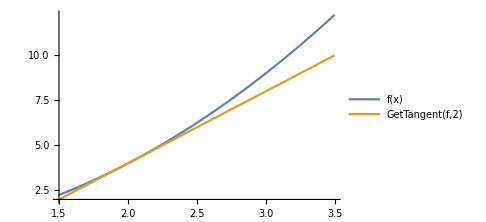

```mathematica
Clear[f];f=Function[x,x^2];Plot[{f[x],GetTangent[f,2]},{x,1.5,3.5},ImageSize->Medium,PlotLegends->"Expressions"]
```

Ver o que ocorre agora em x_3=x_1+0.1.

Em x_3=2.1, o diferencial será 4·0.1=0.4 (não é 4x·0.1, a função secante, é 4·0.1, a derivada slope). Novamente, o diferencial não é a linha, é o incremento. Em x=3, o diferencial é 4·1=4.

```mathematica
GetTangent[Function[x,x^2],2]
```

-4+4 x

Mas estou perdendo o ponto da aplicação do diferencial. O ponto é “reduzir a computação” tomando o incremento da derivada em um ponto próximo do desejado onde se tiraria a derivada exata. Vamos supor, x=3 e um Δx=0.1.
O limite diz que a diferença entre o incremento da função em x=3 com Δx=0.1 e o incremento da derivada em x=3 com Δx=0.1 será um infinitesimal. E realmente, nada a ver, é só a diferença do incremento entre a função e a derivada, que obviamente convergem no mesmo x.
Bem, o incremento da função é Δy=f(x+Δx)-f(x)=... não vou nem usar essa “maldita” fórmula. Em  x=3.1, y=3.1^2=9.61. Em x=3, y=9. O incremento foi de 0.61.
Já a derivada (slope) em x=3 é 2x(3)=6. Isso significa que sua função secante é s(x)=6x. Esta secante está em qualquer abscissa x, o incremento é independente disto. O incremento de 6x (obviamente em Δx=0 é 0) em Δx=0.1 é... também não vamos usar a fórmula do incremento. Em x=3.1, y=6x(3.1)=18.6. Em x=3, y=18, o incremento é 0.6.

```mathematica
3.1^2
```

9.61

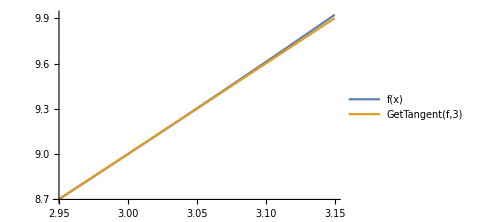

```mathematica
Clear[f];f=Function[x,x^2];Plot[{f[x],GetTangent[f,3]},{x,2.95,3.15},ImageSize->Medium,PlotLegends->"Expressions"]
```

Está certinho. Vamos ver alguns incrementos (de f').

```mathematica
Table[Function[{x0,deltax},6*(x0+deltax)-6*x0][3,deltax],{deltax,{0,0.0001,0.001,0.01,0.1,1}}]
```

{0,0.0006,0.006,0.06,0.6,6}

3.5

Para “plotar” o diferencial , é preciso reconstituir sua reta. Ela tangencia em x_0=3.
Aqui, a secante é 6x. Em x=3, y=18. A função f, em x=3, tem y=9. Vamos acrescentar -9 à secante: 6x-9.

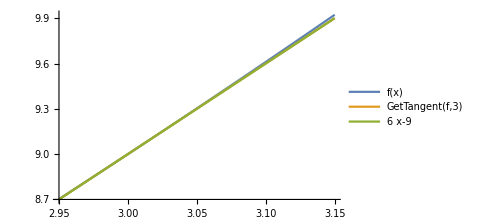

```mathematica
Clear[f];f=Function[x,x^2];Plot[{f[x],GetTangent[f,3],6x-9},{x,2.95,3.15},ImageSize->Medium,PlotLegends->"Expressions"]
```

Vamos ver algumas diferenças entre incrementos de f e f'.

```mathematica
Table[Function[{x0,deltax},((x0+deltax)^2-x0^2)-(6*(x0+deltax)-6*x0)][3,deltax],{deltax,{0,0.0001,0.001,0.01,0.1,1}}]
```

{0,1.×10^-8,1.×10^-6,0.0001,0.01,1}

De acordo com esta tabela, a diferença entre x={3,4} nos incrementos é de 1.

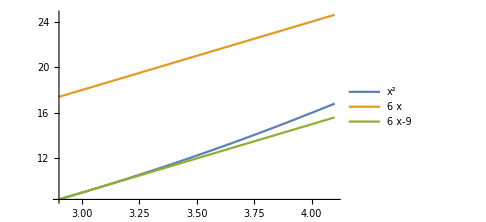

```mathematica
Clear[f];f=Function[x,x^2];Plot[{x^2,6x,6x-9},{x,2.9,4.1},ImageSize->Medium,PlotLegends->"Expressions"]
```

```mathematica
(16-9)-(15-9)
```

1

O incremento da derivada é independente do tangenciamento portanto devia bater.
O quê está errado? Em x_0=3, f(3)=9; f(4)=16. Δy=7.
f'(3)=6. s3=6x. s3(3)=18; s3(4)=24. dy=6.
7-6=1. É o gráfico que não bate. E eu que tinha “medido com os olhos” errado.

Plotar o diferencial não é apenas plotar a derivada: apenas porque o diferencial usa um Δx (mas ele é essa derivada com esse Δx). Logo plotar a comparação da derivada com o diferencial (que são diferentes) é plotar duas derivadas, uma com Δx no limite em 0, e outra com Δx>0. (É uma derivada e uma razão.)

Plotar o diferencial é plotar a derivada, porque ele é o(s) incremento(s) da derivada. Tomar um incremento destes ≠0 e tomar seu Δx≠0 e montar o ratio, ou seja, o slope de uma nova reta, é plotar a “nova reta montada a partir do diferencial”, que não é o diferencial. Essa reta é como a derivada, uma razão/slope, mas tomada com uma diferença; enquanto que a derivada é tomada sem diferença.

```mathematica
deriv
```

Function[{f,x0},lim_(x1→x0) incrratio[f,x0,x1]]

```mathematica
incr
```

Function[{f,x0,x1},f[x1]-f[x0]]

```mathematica
incrratio
```

Function[{f,x0,x1},incr[f,x0,x1]/(x1-x0)]

```mathematica
deriv[Function[x,x^2],3]
```

6

```mathematica
MakeSlope[6][x]
```

6 x

Ou seja (passos):
1) Calcular a derivada em um x_0.
2) Tangenciar e plotar a derivada.
3) Tomar um Δx≠0.
4) Calcular um novo ratio do incremento em y de f sobre o incremento em x de f; mas agora sem o incremento tender a zero, mas sim ser sobre o intervalo Δx.
5) Tangenciar este slope em y=f(x_0).
6) Plotar esta tangente.

```mathematica
incrratio[Function[x,x^2],3,0.1]
```

3.1

Podemos fazer uma GetTangent mais geral; passando qual incremento.

```mathematica
Clear[GetAnyTangent]
GetAnyTangent[f_,fsec_,x0_]=Module[{s,ydif,t},	
	s=MakeSlope[fsec];
	ydif=f[x0]-s[x0];
	t=s[x]+ydif;
	t
];
```

```mathematica
Clear[f,ftd,fti];
f=Function[x,x^2];
ftd=GetAnyTangent[f,f'[3],3]
fti=GetAnyTangent[f,incrratio[f,f'[3],0.1],3]
```

-9+6 x

-9.3+6.1 x

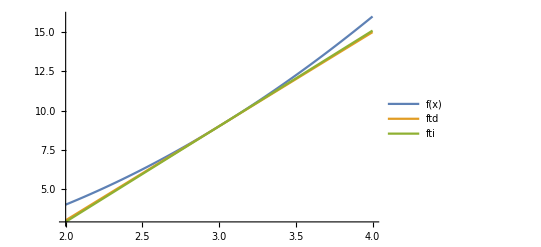

```mathematica
Plot[{f[x],ftd,fti},{x,2,4},PlotLegends->"Expressions"]
```

```mathematica
Clear[if1]
if1=Table[GetAnyTangent[f,incrratio[f,f'[3],i],3],{i,{0.1,0.2,0.3,0.6,1,1.7}}]
```

{-9.3+6.1 x,-9.6+6.2 x,-9.9+6.3 x,-10.8+6.6 x,-12+7 x,-14.1+7.7 x}

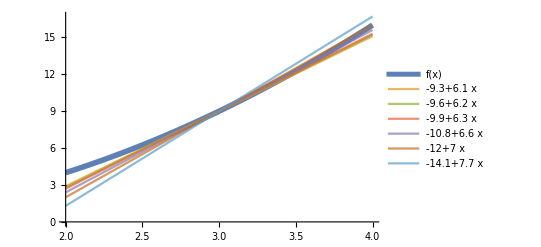

```mathematica
Plot[{f[x],if1},{x,2,4},PlotLegends->"Expressions",PlotStyle->Prepend[Table[s,100],m]]
```

```mathematica
Clear[PltDerAndIncrs];
PltDerAndIncrs=Function[{f,x0,incrs,radius},
	Module[{incrfs},
		incrfs=Table[
			GetAnyTangent[f,incrratio[f,f'[x0],i],x0],
			{i,incrs}
		];
		Plot[
			{f[x],incrfs},
			{x,x0-radius,x0+radius},
			PlotLegends->"Expressions",
			PlotStyle->Prepend[Prepend[Table[
				Directive[Opacity[.5],Thickness[.002]]
				,100],
				Directive[Opacity[1],Thickness[.0075],LineColor->Gray]],
				Directive[Opacity[1],Thickness[.01]]
			],
			ImageSize->Medium
		]
	]
];
```

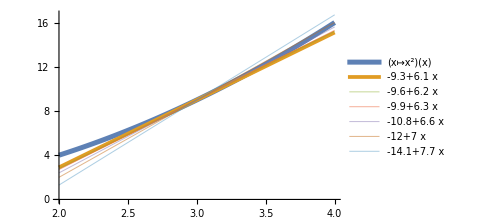

```mathematica
PltDerAndIncrs[Function[x,x^2],3,{0.1,0.2,0.3,0.6,1,1.7},1]
```

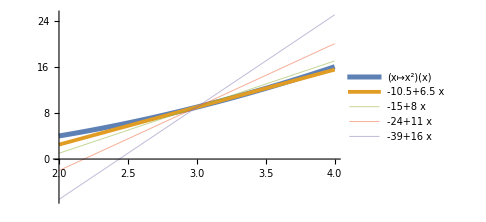

```mathematica
PltDerAndIncrs[Function[x,x^2],3,{0.5,2,5,10},1]
```

Unisul.
A diferencial (não é “o” diferencial) de x é Δx.
A diferencial de y não é Δy.
Δy é o incremento e é y_1-y_0=f(x+Δx)-f(x).
A diferencial de y é dy=y'Δx.
dy/dx=f' porque dy=f'dx=f'Δx.

### Concepção original de Leibniz

O incremento dx é um infinitesimal único. Em função desse incremento, temos o incremento dy na imagem da função, de forma que a razão (assim como na derivada) é dy/dx. Se essa razão é infinitesimalmente pequena, ela pode ser considerada igual a f'(x). Essa razão, porém, não é infinitesimal (é um número real)1. Definição da derivada como apenas esta razão (o limite da razão ainda não fazia parte da definição).

Cauchy, o incremento agora varia; no limite do incremento zero, temos a derivada. dy=f'(x)dx⇒
f'(x)=dy/dx.
O diferencial é definido a partir da derivada. dy e dx são números reais, e não mais infinitesimais.

### Redução

A relação entre derivação e integração. A derivação é o limite do slope conforme Δx tende a zero, a integração é o limite da área conforme Δx tende a zero. Qual a relação entre o slope e a área? O slope é a linha diagonal de um retângulo, e a área, o produto dos lados. Ou o slope é a hipotenusa e a área, o produto dos catetos: triângulo.
Fato que a diagonal do quadrado de lado 1 é irracional.

### Como funções

Ambos números são sobre x_0, ou seja df(x), f'(x).

1	Wikipedia (https://en.wikipedia.org/wiki/Differential_of_a_function)